## Mathematical model of bone expansion during skull morphogenesis

Supplement to the paper:
Self-propagating wave drives morphogenesis of skull bones in vivo
Yiteng Dang, Johanna Lattner, Adrian A. Lahola-Chomiak, Diana Alves Afonso, Elke Ulbricht, Anna Taubenberger, Steffen Rulands, Jacqueline M. Tabler

## Set up model

```mathematica
Clear["Global`*"]
```

### Parameters

Model parameters
ρdA, ρdB: Carrying capacities of A and B cells
D: Diffusion constant
eO, eM: Stiffnesses of cell types A and B
τ: Relaxation timescale of the growth rate
η: Viscosity
γ: Friction
α: Proportionality constant in definition of differentiation rate k_D
ρh: Homeostatic density, at which the pressure is zero
aρ, a: Steepness of the initial profile for ρ and ϕ respectively

System size parameter
L: domain size in microns
tmax: simulation time in hours
Nx: number of steps in the space discretization
T:  number of steps in the time discretization

Recommendations
* Generally, the solvers may work well for certain sets of parameters, but break for others.
* Changing system size parameters may cause simulations to break down (e.g. increasing tmax while keeping T constant).
* It is required that ρ_h > ρ_A, ρ_B in order to get reasonable results for the velocity, so we get the pressure P>0 everywhere. 
* Tune γ to tune the overall speed of individual cells 
* Tune α to tune the expansion speed without affecting V

```mathematica
(* Convert units to hours and μm *)
PaToNewUnits=1/(10^(6)*(1/3600)^2); 
SecToHr = 1/3600;
(* Define all parameters *) (*params={ρdA->0.0067,ρdB->0.0077,D1->15,eO->1000*PaToNewUnits,eM->30*PaToNewUnits,τ->10,η->10^3*PaToNewUnits*SecToHr,γ->0.8*10^3*PaToNewUnits*SecToHr,α->5*10^(-6),ρh->1/1000,aρ->4,a->4}; *)
params={ρdA->0.0067,ρdB->0.0077,D1->15,eO->1000*PaToNewUnits,eM->30*PaToNewUnits,τ->10,η->10^3*PaToNewUnits*SecToHr,γ->0.8*10^3*PaToNewUnits*SecToHr,α->3.5*10^(-6),ρh->1/1000,aρ->4,aϕ->4}; 
(* Simulation settings*)
L=1500;
tmax=8;
Nx=200;
T=100;
```

#### Initial conditions

```mathematica
ρ0[x_]:=(Tanh[aρ x/L]+1)/2 (ρdA-ρdB)+ ρdB;
ϕ0[x_]:=(1-Tanh[aϕ x/L])/2;
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
```

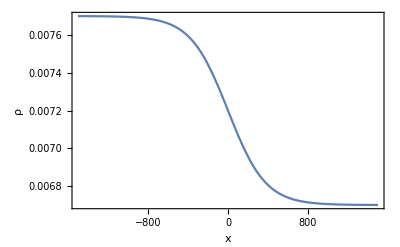
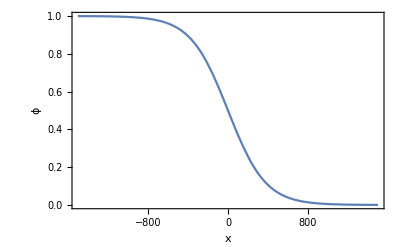

```mathematica
{Plot[{ρ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ρ"}], Plot[{ϕ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ϕ"}]}
```

#### PDE system

```mathematica
(* Define compound variables *)
(* Net growth rates *)
kA:=1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
(* Stiffness *)
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]);
(* Differentiation rates *)
kD:=α (e-eM);
```

```mathematica
(* Define PDE system *)
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-γ v[x,t])==e D[ρ[x,t],x] + D[e, x] Log[ρ[x,t]/ρh]*ρ[x,t] };
vars={ρ,ϕ,v};
fullsys=Join[PDEsys/.params,bc,iv]
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (14.9254 (0.0067-ρ[x,t]) (1-ϕ[x,t])+12.987 (0.0077-ρ[x,t]) ϕ[x,t]),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-14.9254 (0.0067-ρ[x,t])+12.987 (0.0077-ρ[x,t])) (1-ϕ[x,t]) ϕ[x,t]+3.5×10^-6 (1-ϕ[x,t]) (-1944/5+1944/5 (1-ϕ[x,t])+12960 ϕ[x,t])+(15 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+15 ϕ^(2,0)[x,t],ρ[x,t] (-2.88 v[x,t]+18/5 v^(2,0)[x,t])==(1944/5 (1-ϕ[x,t])+12960 ϕ[x,t]) ρ^(1,0)[x,t]+62856/5 Log[1000 ρ[x,t]] ρ[x,t] ϕ^(1,0)[x,t],ρ[-1500,t]==0.00769966,ρ[1500,t]==0.00670034,ϕ[-1500,t]==1/2 (1+Tanh[4]),ϕ[1500,t]==1/2 (1-Tanh[4]),v[-1500,t]==0,v[1500,t]==0,ρ[x,0]==0.0077-0.0005 (1+Tanh[x/375]),ϕ[x,0]==1/2 (1-Tanh[x/375]),v[x,0]==0}

## Simulate discretized model

We have implemented multiple discretizations of the PDE system, differing in the definitions of the first and second order spatial and time derivates.

### Define discretized PDE system

```mathematica
PDEsys
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+D1 ϕ^(2,0)[x,t],ρ[x,t] (-γ v[x,t]+η v^(2,0)[x,t])==(eM (1-ϕ[x,t])+eO ϕ[x,t]) ρ^(1,0)[x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM ϕ^(1,0)[x,t]+eO ϕ^(1,0)[x,t])}

```mathematica
(* Equations for PDE *)
(* Time derivative*)
discretizationT={Derivative[0,1][ρ][x,t]->  (Subscript[ρ, i,m+1]-Subscript[ρ, i,m])/Δt, Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt}; (* forward scheme*)

(* 1. forward Euler schemes*)
(* a. explicit scheme, centered diff *)
discretization1 = 
{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx), ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,
v[x,t]-> Subscript[v, i,m], Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx),Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2};
pdeDiscretized1 = PDEsys /.discretizationT /. discretization1;

(* b. explicit scheme, fwd diff *)
(*discretization1b = {ϕ[x,t]-> Subscript[ϕ, i,m], ϕ^(0,1)[x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,ϕ^(1,0)[x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i,m])/(2 Δx),ϕ^(2,0)[x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], V^(2,0)[x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};  
pdeDiscretized =PDEsys /.discretizationT /. discretization1b;*) 

(* 2. backward Euler scheme *) 
(* implicit scheme, centered diff *)
(* NB cannot use implicit scheme for equation for V*)
discretization2 = Join[{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx),ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2}/.{m->m+1}, {v[x,t]-> Subscript[v, i,m],Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx), Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2}];

pdeDiscretized2 =Join[ PDEsys[[;;2]]/.discretizationT /. discretization2, {PDEsys[[3]]/.discretizationT /. discretization1}];

(* 3. Crank-Nicolson scheme: combine discretizations *)
discretization3= {ρ[x,t]->( Subscript[ρ, i,m] + Subscript[ρ, i,m+1])/2, Derivative[1,0][ρ][x,t]-> ((Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx)+(Subscript[ρ, i+1,m+1]-Subscript[ρ, i-1,m+1])/(2 Δx))/2,ϕ[x,t]-> (Subscript[ϕ, i,m]+Subscript[ϕ, i,m+1])/2, Derivative[1,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx)+(Subscript[ϕ, i+1,m+1]-Subscript[ϕ, i-1,m+1])/(2 Δx))/2,Derivative[2,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2+(Subscript[ϕ, i+1,m+1]- 2 Subscript[ϕ, i,m+1] + Subscript[ϕ, i-1,m+1])/(Δx)^2)/2,
v[x,t]-> (Subscript[v, i,m]+Subscript[v, i,m+1])/2,Derivative[1,0][v][x,t]-> ((Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx)+(Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx))/2, Derivative[2,0][v][x,t]->( (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2+(Subscript[v, i+1,m+1]- 2 Subscript[v, i,m+1] + Subscript[v, i-1,m+1])/(Δx)^2)/2};
```

Upwind scheme
Use upwind scheme for stability. See https://en.wikipedia.org/wiki/Upwind_scheme 
Idea here is just to replace derivatives in for the advection terms by upwind terms while keeping the rest the same. 
Warning: This may be very slow to solve.

```mathematica
(*  4. Upwind scheme for 1st derivaties *)
(*upwind1 = {ρ^(1,0)[x,t]-> (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx, v^(1,0)[x,t]-> (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx, ϕ^(1,0)[x,t]-> (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx};*)

PDEsysUpwind=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 
PDEsysUpwind1b=
{Derivative[0,1][ρ][x,t]+ρ[x,t] Derivative[1,0][v][x,t]+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

(*upwind2 = {ρ^(1,0)[x,t]-> (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx), v^(1,0)[x,t]-> (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx), ϕ^(1,0)[x,t]-> (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)}; (* 2nd order upwind*) *)
PDEsysUpwind2=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx)+v[x,t] (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx)==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

pdeDiscretized4 =PDEsysUpwind /. discretization1 /.discretizationT;
pdeDiscretized4b =PDEsysUpwind1b/. discretization1 /.discretizationT;
pdeDiscretized42 =PDEsysUpwind2 /. discretization1 /.discretizationT;
pdeDiscretized4
```

{((-v_(-1+i,m)+v_(i,m)) ρ_(i,m))/Δx+(v_(i,m) (-ρ_(-1+i,m)+ρ_(i,m)))/Δx+(-ρ_(i,m)+ρ_(i,1+m))/Δt==ρ_(i,m) (((ρdA-ρ_(i,m)) (1-ϕ_(i,m)))/(ρdA τ)+((ρdB-ρ_(i,m)) ϕ_(i,m))/(ρdB τ)),(v_(i,m) (-ϕ_(-1+i,m)+ϕ_(i,m)))/Δx+(-ϕ_(i,m)+ϕ_(i,1+m))/Δt==(-(ρdA-ρ_(i,m))/(ρdA τ)+(ρdB-ρ_(i,m))/(ρdB τ)) (1-ϕ_(i,m)) ϕ_(i,m)+α (1-ϕ_(i,m)) (-eM+eM (1-ϕ_(i,m))+eO ϕ_(i,m))+(D1 (-ρ_(-1+i,m)+ρ_(1+i,m)) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(4 Δx^2 ρ_(i,m))+(D1 (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2,ρ_(i,m) (-γ v_(i,m)+((v_(-1+i,m)-2 v_(i,m)+v_(1+i,m)) (ηM (1-ϕ_(i,m))+ηO ϕ_(i,m)))/Δx^2)==f+((-ρ_(-1+i,m)+ρ_(1+i,m)) (eM (1-ϕ_(i,m))+eO ϕ_(i,m)))/(2 Δx)+Log[(ρ_(i,m))/ρh] ρ_(i,m) (-(eM (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)+(eO (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx))}

Choose discretization

```mathematica
(* Choose discretization out of above options *)
pdeDiscretized = pdeDiscretized1;
Simplify[pdeDiscretized/.params]
```

{((-2 Δx-Δt v_(-1+i,m)+Δt v_(1+i,m)) ρ_(i,m)+2 Δx ρ_(i,1+m)+Δt v_(i,m) (-ρ_(-1+i,m)+ρ_(1+i,m)))/(2 Δt Δx)==1.93836 ρ_(i,m) (0.05159-7.15955×10^-18 ϕ_(i,m)+ρ_(i,m) (-7.7+1. ϕ_(i,m))),-(0.5 (7.5 ρ_(-1+i,m)+(30.+Δx v_(i,m)) ρ_(i,m)-7.5 ρ_(1+i,m)) ϕ_(-1+i,m))/(Δx^2 ρ_(i,m))+(-0.0439992-1./Δt+30./Δx^2) ϕ_(i,m)+0.0439992 ϕ_(i,m)^2+ρ_(i,m) ϕ_(i,m) (-1.93836+1.93836 ϕ_(i,m))+(1. ϕ_(i,1+m))/Δt-(15. ϕ_(1+i,m))/Δx^2+(0.5 v_(i,m) ϕ_(1+i,m))/Δx+((3.75 ρ_(-1+i,m)-3.75 ρ_(1+i,m)) ϕ_(1+i,m))/(Δx^2 ρ_(i,m))==0,(64.8 (-0.0444444 (-1.25 v_(-1+i,m)+(2.5+1. Δx^2) v_(i,m)-1.25 v_(1+i,m)) ρ_(i,m)+Δx (ρ_(-1+i,m) (3+97 ϕ_(i,m))-ρ_(1+i,m) (3+97 ϕ_(i,m))+97 Log[1000 ρ_(i,m)] ρ_(i,m) (ϕ_(-1+i,m)-ϕ_(1+i,m)))))/Δx^2==0}

### Solve discretized system: initialization

Next, the system is solved on a grid defined by meshes in x and t. Then the system is solved by looping over time. At a given time t, the profile for V is solved for with the profiles for ρ and ϕ of the same time point t, then the solutions for ρ and ϕ are obtained for the next timestep t+1, followed by solving for V at time t+1, and so on.

```mathematica
(*Define mesh*)
(*
Nx=200;
T= 100;
*)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;

xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

15.

0.08

Check CFL condition (https://en.wikipedia.org/wiki/Courant%E2%80%93Friedrichs%E2%80%93Lewy_condition)
Typically C=(u Δt)/Δx ≤ C_max with C_max=1.
The velocity u needs to be estimated.

```mathematica
vmax=20; (*estimation of max velocity*)
N[ ((ρdA+ρdB)/2/.params)  ΔtSet/ΔxSet] (* ρ[x,t] v^(1,0)[x,t]*)
N[ vmax  ΔtSet/ΔxSet] (*v[x,t] ρ^(1,0)[x,t]*) (*v[x,t] ϕ^(1,0)[x,t]*)
```

0.0000384

0.106667

```mathematica
(* Boundary conditions *)
ρL=ρ0[-L] /. params; ρR=ρ0[L] /. params; 
(*ϕL = 1; ϕR = 0;*)
ϕL=ϕ0[-L]/.params; ϕR=ϕ0[L]/.params;
VL=0; VR=0;

(* normal *)
bcρ={Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR};
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR};
bcρRepl={Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR};

(* 2nd order upwind *)
bcρ2={Subscript[ρ, -1,m]==ρL,Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR,Subscript[ρ, Nx+1,m]==ρR};
bcϕ2={Subscript[ϕ, -1,m]==ϕL,Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR,Subscript[ϕ, Nx+1,m]==ϕR};
bcV2={Subscript[v, -1,m]==VL,Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR,Subscript[v, Nx+1,m]==VR};
bcρRepl2={Subscript[ρ, -1,m]-> ρL,Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR,Subscript[ρ, Nx+1,m]->ρR};
bcϕRepl2={Subscript[ϕ, -1,m]-> ϕL,Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR,Subscript[ϕ, Nx+1,m]->ϕR};
bcVRepl2={Subscript[v, -1,m]-> VL,Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR,Subscript[v, Nx+1,m]->VR};

(* Initial conditions *)
ρ0Set=Table[ ρ0[ xmesh[[i]] ] , {i,1,Nx+1}] /. params;
(*ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];*)
ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,1, Nx+1}] /. params; 

(* Initialize values *)
ρAll=Table[Subscript[ρ, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[v, i,m], {i, 0, Nx}, {m, 0, T}];

(* set initial values*)
Do[ρAll[[i+1, 1]] =ρ0Set[[i+1]], {i,0,Nx}]; 
Do[ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 

(* set Dirichlet boundary values *)
Do[ρAll[[1, j+1]] = ρL, {j, 0, T}]
Do[ρAll[[Nx+1, j+1]] = ρR, {j, 0, T}]
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
```

```mathematica
(* Only for Crank-Nicolson: initial values for V*)
(*
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
*)
```

```mathematica
Do[
Print[thism];
(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=Simplify@(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)

(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals, Method->"Homotopy"];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
],
{thism, 0, T}];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

## Plot simulation results

#### Full results as heatmaps

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full};plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

#### Partial results

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full};
tstop=10;
ρAllPart = ρAll[[;;, 1;;tstop]];
ϕAllPart =ϕAll[[;;, 1;;tstop]];
VAllPart=VAll[[;;, 1;;tstop]];
plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

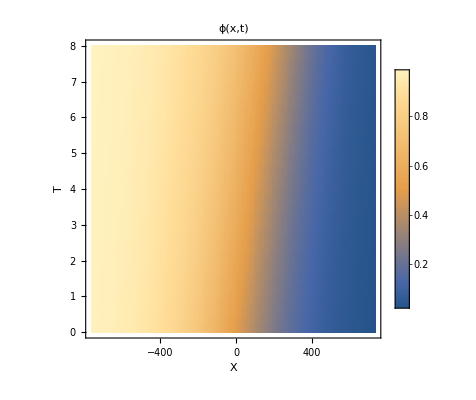

```mathematica
(*Zoom in*)
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,Round[Nx/4],Round[Nx*3/4]}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

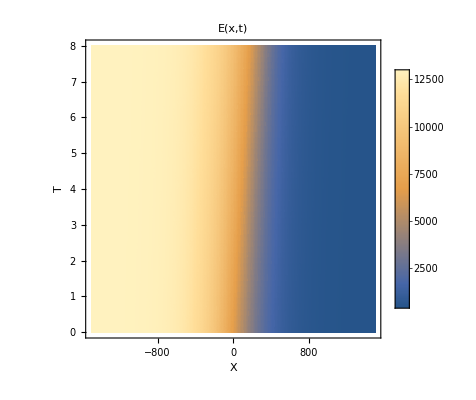

```mathematica
(*Plot stiffness*)
plotDataE=Flatten[Table[ {xmesh[[i]], tmesh[[j]],(eM(1-ϕAll[[i,j]])+eO ϕAll[[i,j]]) /. params}, {i,1, Nx+1}, {j,1, T+1}],1];ListDensityPlot[plotDataE, PlotLabel-> "E(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

### Plot snapshots

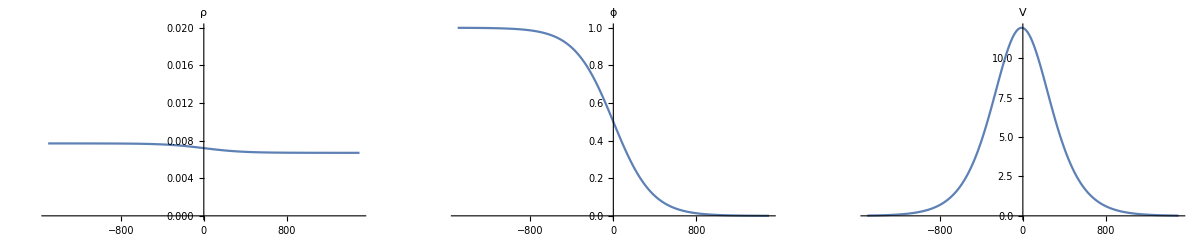

```mathematica
(* Plot as separate graphs *)
tplot= 1; (*Index of time point to plot*)
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}};
p1=ListPlot[  Transpose[{xmesh, ρAll[[;;, tplot]]}], Joined-> True , PlotRange-> {Automatic, {0, 0.02}}, PlotLabel->"ρ", plotOptions];
p2=ListPlot[  Transpose[{xmesh, ϕAll[[;;, tplot]]}], Joined-> True, PlotRange-> {Automatic, {0, 1}},PlotLabel->"ϕ",plotOptions];
p3=ListPlot[  Transpose[{xmesh, VAll[[;;, tplot]]}], Joined-> True, PlotLabel->"V",plotOptions];
GraphicsRow[{p1,p2,p3}, ImageSize->Full]
(*Show[p1,p2,p3, PlotRange-> All]*)
```

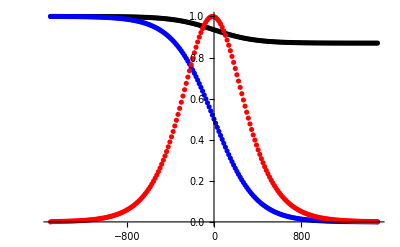

```mathematica
(* Plot together in same graph *)
tplot= 1;
p1=ListPlot[ Transpose[{xmesh,ρAll[[;;,tplot]]/Max[ρAll[[;;,tplot]]]}], PlotStyle-> {Black} ];
p2=ListPlot[ Transpose[{xmesh,ϕAll[[;;,tplot]]/Max[ϕAll[[;;,tplot]]]}], PlotStyle-> {Blue} ];
p3=ListPlot[ Transpose[{xmesh,VAll[[;;,tplot]]/Max[VAll[[;;,tplot]]]}], PlotStyle-> {Red}, PlotRange->All ];
Show[ p1, p2, p3, PlotRange-> All, AxesOrigin-> {0,0}]
```

### Plot together with experimental data

#### Plot average interface position

According to position of ϕ

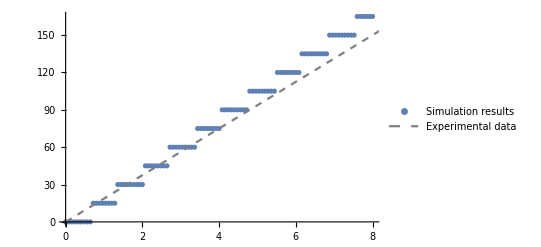

```mathematica
indices=Flatten@Map[ FirstPosition[#, True]&, Transpose@Map[  (#<0.5)&, ϕAll, {2}  ]];
positions = Map[ xmesh[[#]]&, indices]-xmesh[[indices[[1]]]];

p1=ListPlot[ Transpose[{tmesh, positions}], PlotLegends-> {"Simulation results"} ];
p2=ListPlot[{{tmesh[[-1]], positions[[-1]]}, {tmesh[[1]],  positions[[1]]}}, Joined-> True, PlotStyle->Dashed, PlotLegends-> {"Fit through first and last data points"}];
(*p3=ListPlot[{{0, 0}, {4, 75}}, Joined-> True, PlotStyle->{Dashed, Gray}]; *)
p3=Plot[75/4 x,{x,0,T}, PlotStyle->{Dashed, Gray}, PlotLegends-> {"Experimental data"}];(*experiments est.*)
Show[p1,p3 ]
```

According to position of V (peak)

```mathematica
indices2=Flatten@Table[ Position[ VAll[[;;,ti]], Max@VAll[[;;,ti]] ], {ti, 1, T+1}];
positions2 = Map[ xmesh[[#]]&, indices2]-xmesh[[indices2[[1]]]];
```

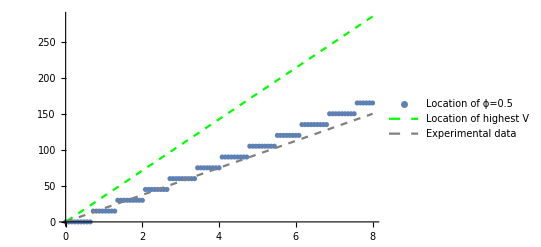

```mathematica
p1=ListPlot[ Transpose[{tmesh, positions}], PlotLegends-> {"Location of ϕ=0.5"}];
p2=ListPlot[{{tmesh[[-1]], positions[[-1]]}, {tmesh[[1]],  positions[[1]]}}, Joined-> True, PlotStyle->Dashed];
p2b=ListPlot[{{tmesh[[-1]], positions2[[-1]]}, {tmesh[[1]],  positions2[[1]]}}, Joined-> True, PlotStyle->{Green,Dashed}, PlotLegends-> {"Location of highest V"}];
p3=Plot[75/4 x,{x,0,tmax}, PlotStyle->{Dashed, Gray}, PlotLegends-> {"Experimental data"}];(*experiments est.*)
Show[p1,p2b,p3, PlotRange-> Full]
```

#### Plot V together with experimental data

```mathematica
(* Load experimental data *)
dataPath = "/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Analysis_scripts/Scripts_R/exp_data/Velocities_means.csv";
data=Import[dataPath, "CSV"];
(* headers=First[data]; (*original headers*) *)
headers={"Location", "X","V","eX","eV"};
rows=Rest[data];
dataset=Dataset[AssociationThread[headers,#]&/@rows];
dataset
```

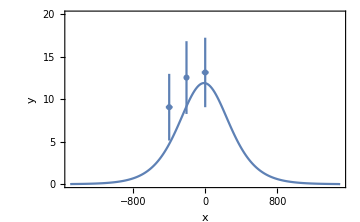

```mathematica
(*Extract data from the DataSet*)
dataList=Normal[dataset];

(*Extract x,y,ex,and ey from the data list*)
plotData=dataList[[All,headers[[2;;]]]];
formattedData={{#X,#V},ErrorBar[#eX,#eV]}&/@plotData;

(*Create the error bar plot*)
ebPlot =ErrorListPlot[formattedData,PlotTheme->"Detailed",AxesLabel->{"x","y"},PlotMarkers->Automatic,GridLines->None, PlotRange->{{-L, L}, {0, 20}}];
vPlot=ListPlot[  Transpose[{xmesh, VAll[[;;, tplot]]}], Joined-> True, PlotLabel->"V",plotOptions];
Show[ebPlot, vPlot]
```

### Save results

Save simulation results as separate CSV files for the list of parameters, ρ, ϕ and V.

```mathematica
(*Save path and filename pattern*)
filenamePattern=DateString[{"ISODate","_", "Hour", "Minute"}]; (* use current date and time*)
OutNameRoot =FileNameJoin[{NotebookDirectory[], "Model_results", filenamePattern}]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1806

```mathematica
allParams={eO,eM,η,γ,τ,D1,α,ρdA,ρdB,ρh,aρ,aϕ,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
```

```mathematica
(* Export parameters*)
(*AllParams=Join[ params, {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T, "Dirichlet Boundaries"}]*)
allParams={eO,eM,η,γ,τ,D1,α,ρdA,ρdB,ρh,aρ,aϕ,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
Export[StringJoin[OutNameRoot, "_data_parameters.csv"], allParamsOut, "csv"]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1806_data_parameters.csv

```mathematica
(*dataSave =Map[DecimalForm[#, dec]&, N[ρAll, dec], {2}];*)
Clear[dataSave];dataSave = N[ρAll]// TableForm;
Export[StringJoin[OutNameRoot, "_data_rho_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave = N[ϕAll]// TableForm;
Export[StringJoin[OutNameRoot, "_data_phi_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave =N[VAll] // TableForm;
Export[StringJoin[OutNameRoot, "_data_V_1.csv"], dataSave, "CSV"]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1806_data_rho_1.csv

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1806_data_phi_1.csv

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1806_data_V_1.csv

Save plots

```mathematica
(*
Export[StringJoin[OutNameRoot, "plot_rho_1.eps"], pρ, "EPS"]
Export[StringJoin[OutNameRoot, "plot_phi_1.eps"], pϕ, "EPS"]
Export[StringJoin[OutNameRoot, "plot_V_1.eps"], pV, "EPS"]
*)
```

### Compute single-cell trajectories

Here, we compute the velocity of a single cell starting at a location x using the velocity profile V(x, t) through
	x(t+1) = x(t) + v(x(t), t)*Δt.

#### Plot velocity profile

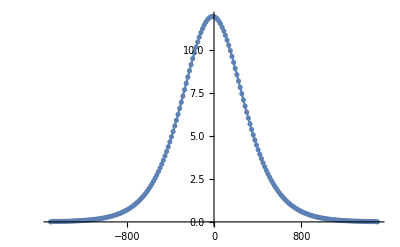

```mathematica
(* Interpolation function*)
idx =1;
dataTmp =Transpose[{xmesh, VAll[[;;, idx]]}];
InterpolationV =Interpolation[ dataTmp, InterpolationOrder->1];
p1=ListPlot[dataTmp ];
p2=Plot[InterpolationV[x], {x, -L , L}];
Show[p1, p2, PlotRange-> All]
```

### Simulate 1 cell

Initial positions to take: 0, -200, -400 μm, corresponding to the locations of the tracked cells.

```mathematica
(*Filename for saving*)
 filenamePattern=DateString[{"ISODate","_", "Hour", "Minute"}]; (* use current date and time*) 
(*filenamePattern="2024-07-19_1141";*)
RootFolder = FileNameJoin[{NotebookDirectory[], "Model_results", StringJoin[filenamePattern, "_1cell"]}];

(*Settings*)
IntOrder=1; (*interpolation order*)
xCell0List = {0, -200, -400};
(*sim=1;*)

xCellAllAll = {};
vCellAllAll = {};

For[sim=1, sim< 4,sim++,
Print[sim];

(* interpolation func*)
xCell0 = xCell0List[[sim]]; (*initial position of tracked cell*)
tIdx =1;
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationV0 =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCell0=InterpolationV0[xCell0];
xCellAll={xCell0};
vCellAll={vCell0};
For[tIdx=2, tIdx≤ T+1, tIdx++,
xCellTmp = xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew =xCellTmp+vCellTmp*ΔtSet;

(* define new interpolation func*)
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationVTmp =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew = InterpolationVTmp[xCellNew];

(* add results to lists *)
AppendTo[xCellAll, xCellNew];
AppendTo[vCellAll, vCellNew];
];

(* Save results *)
AppendTo[xCellAllAll, xCellAll];
AppendTo[vCellAllAll, vCellAll];

settingsToSave={{"xCell0", xCell0},{"IntOrder", IntOrder}};
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_xCellAll.csv"]}], xCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_vCellAll.csv"]}], vCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_settings.csv"]}], settingsToSave, "CSV"];

]
```

1

2

3

```mathematica
q
```

q

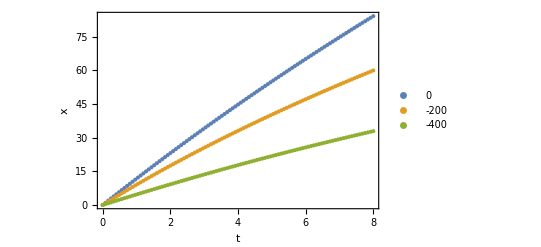

```mathematica
ListPlot[ Table[ Transpose[{tmesh, xCellAllAll[[i,;;]]-xCell0List[[i]]  }], {i, 1, 3}  ],PlotLegends->{ToString/@xCell0List}, Frame-> True, FrameLabel-> {"t", "x"} ]
```

```mathematica
Export[StringJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_xCellAll.csv"]}], xCellAll, "CSV"];
```

## Load saved results

Warning: some of the loaded numbers (stored as fractions) are imported as strings rather than numbers.

```mathematica
filenamePattern = "2024-07-19_1141";
InNameRoot =FileNameJoin[{NotebookDirectory[], "Model_results", filenamePattern}]
ρAll=Import[ StringJoin[InNameRoot, "_data_rho_1.csv"] ];
ϕAll=Import[ StringJoin[InNameRoot, "_data_phi_1.csv"] ];
VAll=Import[ StringJoin[InNameRoot, "_data_V_1.csv"] ];
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/Model_simulation_scripts/Model_results/2024-07-19_1141

```mathematica
parameters =Import[ StringJoin[InNameRoot, "_data_parameters.csv"] ];
params=Thread[ToExpression@parameters[[;;, 1]]-> parameters[[ ;;, 2]] ]

Clear[Nx, tmax, T, L];
Nx=parameters[[ FirstPosition[ Map[#=="Nx"&, parameters[[;;, 1]]], True], 2 ]][[1]];
tmax=parameters[[ FirstPosition[ Map[#=="tmax"&, parameters[[;;, 1]]], True], 2 ]][[1]];
T=parameters[[ FirstPosition[ Map[#=="T"&, parameters[[;;, 1]]], True], 2 ]][[1]];
L=parameters[[ FirstPosition[ Map[#=="L"&, parameters[[;;, 1]]], True], 2 ]][[1]];

ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;

xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

{eO→12960,eM→1944/5,η→18/5,ξ→2.88,τ→10,D1→15,α→1/200000,ρdA→0.0067,ρdB→0.0077,ρh→1/1000,aρ→4,a→4,L→1000,tmax→4,Nx→200,T→100}

```mathematica
parameters
```

{{eO,12960},{eM,1944/5},{η,18/5},{ξ,2.88},{τ,10},{D1,15},{α,1/200000},{ρdA,0.0067},{ρdB,0.0077},{ρh,1/1000},{aρ,4},{a,4},{L,1000},{tmax,4},{Nx,200},{T,100}}

## Systematically calculate v for range of parameter values

This section computes a number of additional quantities from the simulation results.

### Theoretical front velocity

The front velocity for a pulled wave is approximately
	v_F = (D(k_B-k_A) + α(E_B-E_A))^(1/2) + v_A
However, k_A, k_B are not constant. Approximate as (k_A+k_B)/2.

```mathematica
params
```

{eO→12960,eM→1944/5,η→18/5,ξ→2.88,τ→10,D1→15,α→1/200000,ρdA→0.0067,ρdB→0.0077,ρh→1/1000,aρ→4,a→4,1000→1000,4→4,200→200,100→100}

```mathematica
Sqrt[D1(kB-kA) + α (eO-eM)] /. {ρ[x,t]-> (ρdA+ρdB)/2}/.params
```

0.521727

### Calculate Δϕ

Numerically solve for wave velocity by shifting the profile ϕ[x, t] to ϕ[x + v δt, t + δt] and finding v for which the difference | ϕ[x, t] - ϕ[x + v δt, t + δt] | is minimized. 
Do for a range of values of t (denoted t1), but only one δt should be sufficient.

Boundaries: -L <= xp+vp δt <= L, so xp <= L - vp δt, so need to set this as integral / sum upper bound

```mathematica
(* quick calculation, without multiple T*)
(*
t1=20;
δt=10;
vpList=Range[0, 2*δt]/δt;
ΔϕFull=Sum@Table[
Sum[ (ϕAll[[x,t1 ]]-ϕAll[[x+vpList[[vj]] δt, t1+δt]] ), 
{x, 1, Nx-vpList[[vj]] δt}],
{vj, 1, Length[vpList]}
];
*)
```

```mathematica
T
```

100

```mathematica
Nx
```

200

```mathematica
(*Numerically test across a range of values for t and v*)
T1=20;δt=30;
t1All = Range[T1, T-δt, δt]; (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 0.5*δt]/δt;
```

```mathematica
(*Test *)
(*(ϕAll[[x, t]]-ϕAll[[x+vp dt, t+dt]] )/.{x-> Nx/2, t-> T/2, vp-> vpList[[1]],dt -> 10}*)
```

Note: smallest possible difference in v testable is ΔxSet/δt, as the mesh size ΔxSet is fixed.
Testable difference in V (μm/hr):

```mathematica
N[ΔxSet/δt]
```

0.333333

```mathematica
Module[{dt = δt},
ΔϕFull=Abs[
Table[
Sum[ (ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] ), {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, t1len}, {vj, 1, Length[vpList]}
]
];
]
(*ΔϕFull=Table[  NIntegrate[Abs[((ϕsol/.{t->t1, x->xp})-(ϕsol/.{t->t1+δt, x->xp+vp δt} ) )] /.{x->xp} , {xp, -L, L-vp δt}, MaxRecursion->12],  {t1, t1All[[1]], t1All[[-1]], δt }, {vp, vpList[[1]], vpList[[-1]], δvp}];*)
```

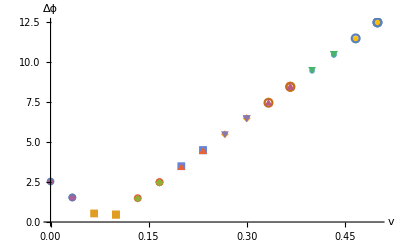

```mathematica
t1temp=ConstantArray[vpList, t1len] ;
plotdata=Partition[  Transpose[ {Flatten@t1temp, Flatten@ΔϕFull} ] , t1len];hplot=ListPlot[plotdata, Frame->False, PlotMarkers->{Automatic, 8},AxesLabel->{Style["v",Black, FontSize-> 20],Style["Δϕ", Black,FontSize-> 20] }, TicksStyle->Directive[Black,16]]
```

```mathematica
(* Save plot *)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/","calculate_v_from_del_phi.eps"];
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "del_phi_convergence_kF_", ToString[kF /. params],"_sM_30_sO_", ToString[sO /. params],"_epsphi_", ToString[ϵϕ],".eps"];*)
(*Export[fnameOut, hplot, "EPS"]*)
```

#### Find optimal v

```mathematica
(*Find minima of Δϕ for each t1*)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]] (*values of velocity where the difference is minimal *)
```

{1/10,1/10}

```mathematica
(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]]  (* "optimal v" *)
```

1/10

```mathematica
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]]
```

0.477958

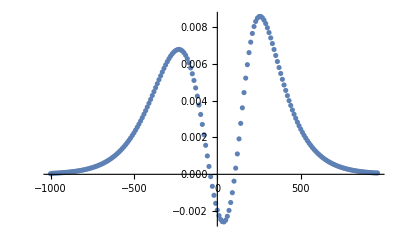

```mathematica
(* Plot difference between profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
δvals=Table[ϕAll[[x, t1 ]]-ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, δvals}],PlotRange-> All,PlotLegends->"Δϕ"]
```

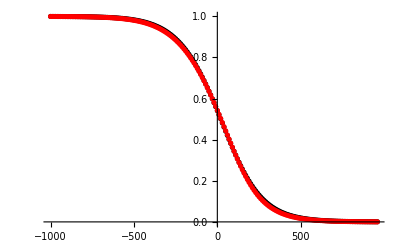

```mathematica
(* Plot both profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
ϕ1vals=Table[ϕAll[[x, t1 ]], {x, 1, Nx-vInferred dt}];
ϕ2vals=Table[ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]

p1=ListPlot[Transpose[{xvals, ϕ1vals}],PlotRange-> All,PlotLegends->"ϕ1", PlotStyle-> {Black}];
p2=ListPlot[Transpose[{xvals, ϕ2vals}],PlotRange-> All,PlotLegends->"ϕ2", PlotStyle-> {Red}];
Show[p1,p2]
```

In units of μm/hr:

```mathematica
N[vInferred*ΔxSet/ΔtSet]
```

25.

### Width of ϕ profile

Obtain by simply setting thresholds ϕ_L≤ ϕ ≤ ϕ_H

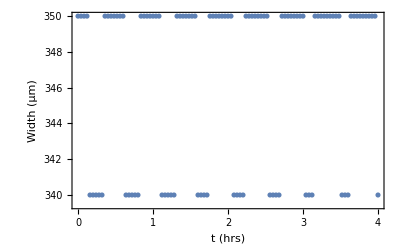

```mathematica
ϕL=0.2; ϕH=0.8;
ϕMid=Boole@Map[(ϕL<#)&& (#<ϕH)&,ϕAll, {2}];
AllWidths=Total[ϕMid]*ΔxSet;

ϕwidth = Mean[ AllWidths[[Round[T/2];;]] ];
ListPlot[ Transpose[{tmesh,AllWidths}] , Frame-> True, FrameLabel->{"t (hrs)", "Width (μm)"}]
```

```mathematica
N[ϕwidth]
```

347.115

### Organize data together and save

Save parameters + inferred v + error Δϕ

```mathematica
params
```

{eO→12960,eM→1944/5,η→18/5,ξ→2.88,τ→10,D1→15,α→1/200000,ρdA→0.0067,ρdB→0.0077,ρh→1/1000,aρ→4,a→4,1000→1000,4→4,200→200,100→100}

```mathematica
(*vars={{τ,ρdA,ρdB,ρh},{D1,α,kF},{fc,ξ,χ,η,κ},{sM,sO,a,τs}};*)
vars = {eO,eM,η,γ,τ,D1,α,ρdA,ρdB,aρ,aϕ,ρh};
varsVals=Map[Replace[#, Flatten@params]&,vars, 2]
```

{12960,1944/5,18/5,2.88,10,15,1/200000,0.0067,0.0077,4,4,1/1000}

deltavUnits:

```mathematica
(*varsOut=ToString/@{{tau,rhoA,rhoB,rhoh},{D1,alpha,kDiff},{fc,xi,chi,eta,kappa},{sM,sO,a,taus},{"xmin", "xmax", "tmax", "deltat", "deltavp"},{"vInferred", "DeltaphiInferred"}}*)
varsOut=ToString/@{{eO,eM,eta,xi,tau,D1,alpha,rhodA,rhodB,aRho,aPhi,rhoh},{"xmin", "xmax", "tmax", "deltat", "deltavUnits"},{"vInferred", "DeltaphiInferred", "vInferredMicrons", "phiWidthMicrons"}}
varsValsOut=N/@Join[varsVals,{{-L,L,tmax,δt,ΔxSet/δt}},{{vInferred, ΔϕInferred, vInferred*ΔxSet/ΔtSet, ϕwidth}}]
```

{{eO, eM, eta, xi, tau, D1, alpha, rhodA, rhodB, aRho, a, rhoh},{xmin, xmax, tmax, deltat, deltavUnits},{vInferred, DeltaphiInferred, vInferredMicrons, phiWidthMicrons}}

{12960.,1944/5,18/5,2.88,10.,15.,1/200000,0.0067,0.0077,4.,4.,1/1000,{-1000.,1000.,4.,30.,0.333333},{0.1,0.477958,25.,347.115}}

```mathematica
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "vdata_kF_", ToString[kF /. params],"_sM_30_sO", ToString[sO /. params],"_es_", ToString[ϵs],"_epsphi_", ToString[ϵϕ],"_t20.csv"]*)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/", "simulation_set3/", "velocity_data.csv"] 
(*Export[fnameOut, {varsOut,varsValsOut}, "CSV"]*)
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/velocity_data.csv

## Solve using NDSolve (not recommended)

```mathematica
ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}]
(*, InterpolationOrder->All, PrecisionGoal-> Infinity, MaxStepSize->30] *)(*, MaxSteps->100000, MaxStepSize->1] *)
```

{{ρ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

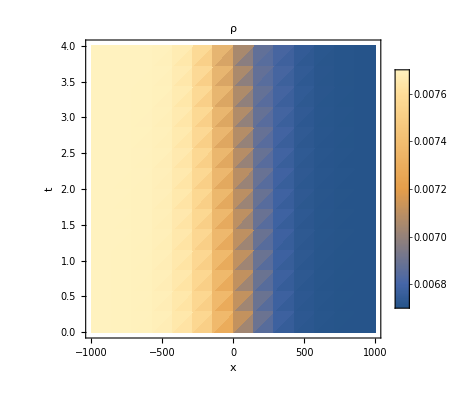
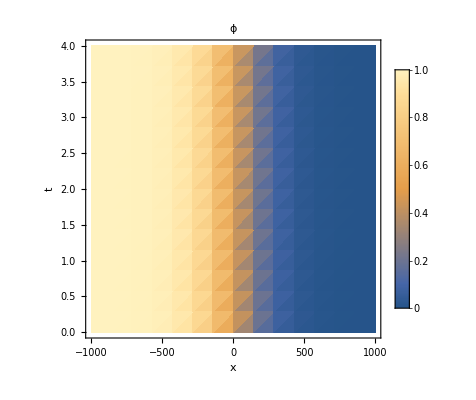
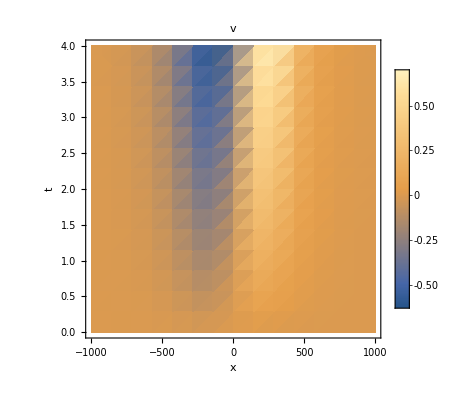

```mathematica
{DensityPlot[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ρ"],
DensityPlot[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ϕ"],
DensityPlot[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"v"]}
```

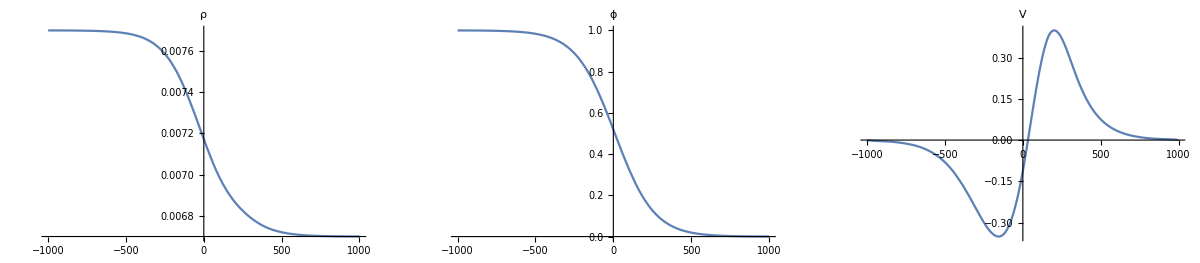

```mathematica
(* Plot a snapshot in time*)
tplot= 2;
p1=Plot[ρ[x,tplot]/.ndsol[[1]], {x, -L, L},PlotRange->All, PlotLabel->"ρ"];
p2=Plot[ϕ[x,tplot]/.ndsol[[1]], {x, -L, L},PlotRange->All, PlotLabel->"ϕ"];
p3=Plot[v[x,tplot]/.ndsol[[1]], {x, -L, L},PlotRange->All, PlotLabel->"V"];
GraphicsRow[{p1,p2,p3}, ImageSize->Full]
```